```mathematica
reversePoints[a_]:=Module[{aux},aux=a;For[i=1,i≤Length[points],i++,aux[[i,1]]=-a[[i,1]]];aux]
```

```mathematica
L=20;a=1;
```

```mathematica
points={{0.5,10},{0.5527781861544074,11.0},{0.7129121894966453,12.0},{0.986121811340027,13.0},{1.0,13.04138126514911},{1.383156030192957,14.0},{1.9222527892982448,15.0},{2.0,15.123475382979798},{2.6345400686718827,16.0},{3.0,16.422616289332566},{3.5773837106674353,17.0},{4.0,17.365459931328118},{4.876524617020201,18.0},{5.0,18.077747210701755},{6.0,18.616843969807043},{6.958618734850891,19.0},{7.0,19.013878188659973},{8.0,19.287087810503355},{9.0,19.447221813845594},{10,19.5}};
```

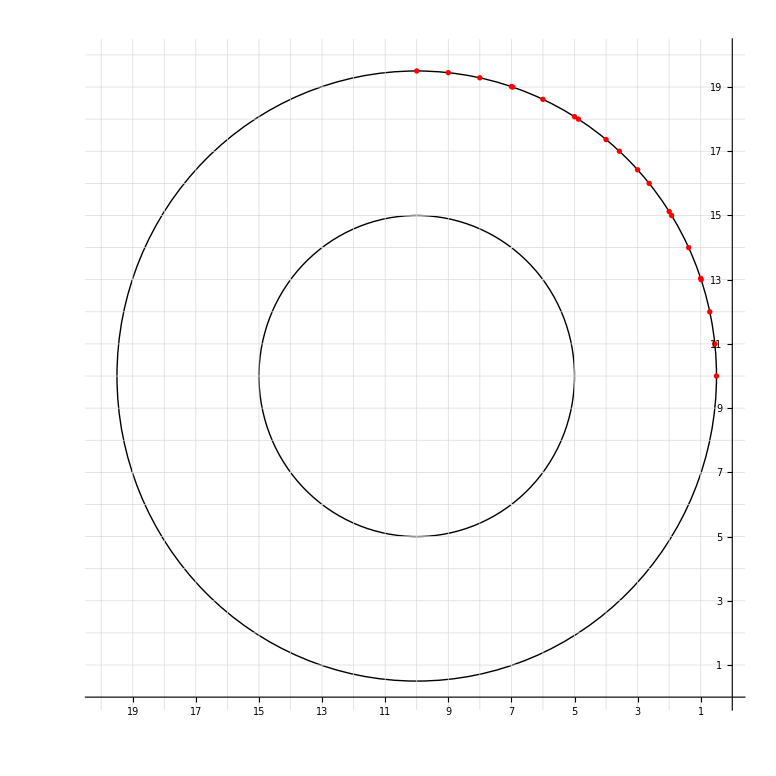

```mathematica
Graphics[{Circle[{-L/2,L/2},(L-a)/2],Circle[{-L/2,L/2},5a],{PointSize->0.005,Red, Point[reversePoints[points]]}},GridLines->{Table[i,{i,-L,0}],Table[i,{i,0,L}]},Axes->True,AxesOrigin->{0,0},PlotRange->{{-L-0.1,0},{0,L+0.1}},Ticks->{Table[{-i,i},{i,1,L}],Table[{i,i},{i,1,L}]}]
```